```mathematica
pdf[g_,gm_]:= 1/10^(gm/10)Exp[-g/10^(gm/10)];
```

RAYLEIGH QAM:

```mathematica
Q[z_]:=1/2 Erfc[z/(√2)];
```

```mathematica
probErrorQAM[g_, α_, M_]:=4/Log[2,M](1-2^((-Log[2,M])/2))Q[√((3 g Log[2,M])/(M-1))];
```

```mathematica
BERRAYQAM[gm_, α_, M_] := Re[Integrate[probErrorQAM[g, α, M]×pdf[g, gm], {g,0,∞}]];
```

```mathematica
PNmRAYQAM[gm_,α_,M_,N_,m_]:=((N!)/(m!(N-m)!))×(1-BERRAYQAM[gm,α, M])^(N-m)×(BERRAYQAM[gm,α, M])^m;
```

```mathematica
PeMRAYQAM[gm_,α_,M_,N_]:= 1 - PNmRAYQAM[gm,α,M,N,0];
```

RAYLEIGH PSK:

```mathematica
probError[g_,α_]:=1/2 Erfc[√(α g)];
```

```mathematica
BERRAY[gm_, α_] := Re[Integrate[probError[g, α]×pdf[g, gm], {g,0,∞}]];
```

```mathematica
PNmRAY[gm_,α_,N_,m_]:=((N!)/(m!(N-m)!))×(1-BERRAY[gm,α])^(N-m)×(BERRAY[gm,α])^m;
```

```mathematica
PeMRAY[gm_,α_,N_]:= 1 - PNmRAY[gm,α,N,0];
```

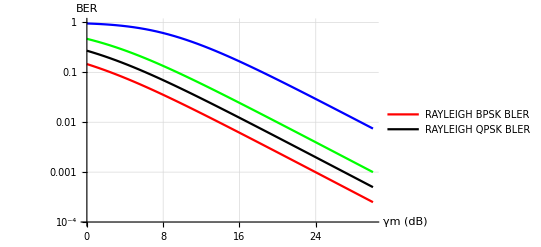

```mathematica
LogPlot[{PeMRAY[x,1, 1], PeMRAY[x,1,2], PeMRAYQAM[x,1,4, 1], PeMRAYQAM[x,1,16, 1]},{x,0,30},AxesLabel->{"γm (dB)","BER"},PlotRange->{10^-4,1}, PlotStyle->{Red, Black, Green, Blue},PlotLegends->{"RAYLEIGH BPSK BLER","RAYLEIGH QPSK BLER"},GridLines->Automatic]
```

BER / BLER AWGN :

```mathematica
BERAWGN[g_, α_] := 1/2 Erfc[√(α 10^(g/10))];
```

```mathematica
BERAWGN[7,1]
```

1/2 Erfc[10^(7/20)]

```mathematica
N[1/2 Erfc[10^(7/20)]]
```

0.000772675

```mathematica
PNmAWGN[g_,α_,N_,m_]:=((N!)/(m!(N-m)!))×(1-BERAWGN[g, α])^(N-m)×(BERAWGN[g, α])^m;
```

```mathematica
PeMAWGN[gm_,α_,N_]:= 1 - PNmAWGN[gm,α,N,0];
```

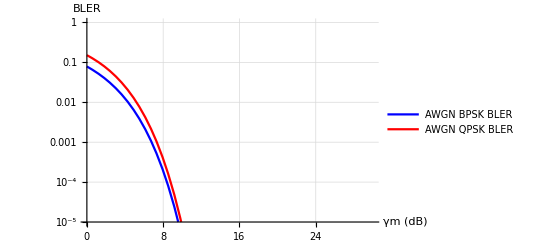

```mathematica
LogPlot[{PeMAWGN[x,1, 1],PeMAWGN[x,1, 2]},{x,0,30},AxesLabel->{"γm (dB)","BLER"},PlotRange->{10^-5,10^0}, PlotStyle->{Blue, Red},PlotLegends->{"AWGN BPSK BLER", "AWGN QPSK BLER","AWGN 16QAM BLER"},GridLines->Automatic]
```

```mathematica
LogPlot[{BERAWGN[x,1],BERAWGN[x,2]},{x,0,30},AxesLabel->{"γm (dB)","BLER"},PlotRange->{10^-8,10^0}, PlotStyle->{Blue, Red},PlotLegends->{"AWGN BPSK BER", "AWGN QPSK BER"},GridLines->Automatic]
```

```mathematica
Q[z_]:=1/2 Erfc[z/(√2)];
```

```mathematica
BERGAUSSBPSK[g_]:=Q[√(2 10^(g/10))];
```

```mathematica
BERGAUSSPSK[g_,M_] :=2/Log[2,M] Q[√(2 10^(g/10)Log[2,M])Sin[π/M]];
```

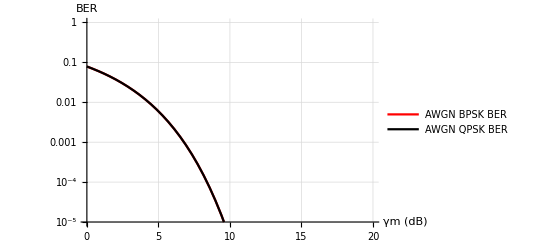

```mathematica
LogPlot[{BERGAUSSBPSK[x],BERGAUSSPSK[x,4]},{x,0,20},AxesLabel->{"γm (dB)","BER"},PlotRange->{10^-5,10^0}, PlotStyle->{Red, Black},PlotLegends->{"AWGN BPSK BER","AWGN QPSK BER"},GridLines->Automatic]
```

```mathematica
PNmAWGNBPSK[g_,N_,m_]:=((N!)/(m!(N-m)!))×(1-BERGAUSSBPSK[g])^(N-m)×(BERGAUSSBPSK[g])^m;
```

```mathematica
PNmAWGNPSK[g_,M_,N_,m_]:=((N!)/(m!(N-m)!))×(1-BERGAUSSPSK[g, M])^(N-m)×(BERGAUSSPSK[g, M])^m;
```

```mathematica
PeMAWGNBPSK[g_,N_]:= 1 - PNmAWGNBPSK[g,N,0];
```

```mathematica
PeMAWGNPSK[g_,M_,N_]:= 1 - PNmAWGNPSK[g,M,N,0];
```

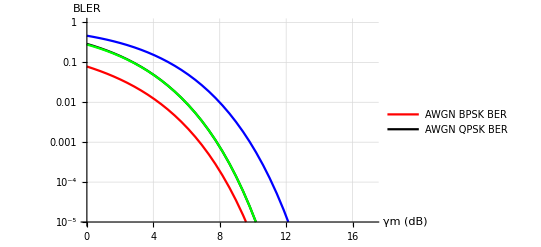

```mathematica
LogPlot[{PeMAWGNBPSK[x,1],PeMAWGNPSK[x,2, 2],PeMAWGNPSK[x,4, 4],PeMAWGNPSK[x,6, 6]},{x,0,20},AxesLabel->{"γm (dB)","BLER"},PlotRange->{10^-5,10^0}, PlotStyle->{Red, Black, Green, Blue},PlotLegends->{"AWGN BPSK BER","AWGN QPSK BER"},GridLines->Automatic]
```

```mathematica
PNmAWGNQAM[g_,M_,N_,m_]:=((N!)/(m!(N-m)!))×(1-BERGAUSSMQAM[g, M])^(N-m)×(BERGAUSSMQAM[g, M])^m;
```

```mathematica
PeMAWGNQAM[g_,M_,N_]:= 1 - PNmAWGNQAM[g,M,N,0];
```

```mathematica
LogPlot[{BERGAUSSPSK[x,2],BERGAUSSPSK[x,4]},{x,0,20},AxesLabel->{"γm (dB)","BLER"},PlotRange->{10^-5,10^0}, PlotStyle->{Red, Black},PlotLegends->{"AWGN BPSK BLER","AWGN QPSK BLER"},GridLines->Automatic]
```

```mathematica
PNmAWGNPSK[g_,M_,N_,m_]:=((N!)/(m!(N-m)!))×(1-BERGAUSSPSK[g, M])^(N-m)×(BERGAUSSPSK[g, M])^m;
```

```mathematica
PeMAWGNPSK[g_,M_,N_]:= 1 - PNmAWGNPSK[g,M,N,0];
```

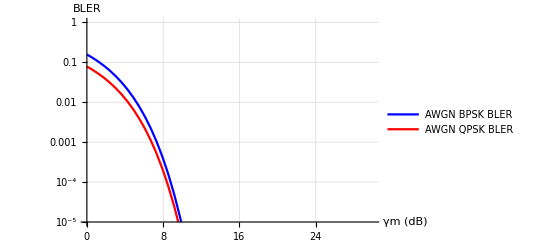

```mathematica
LogPlot[{PeMAWGNPSK[x,2, 1],PeMAWGNPSK[x,4, 1]},{x,0,30},AxesLabel->{"γm (dB)","BLER"},PlotRange->{10^-5,10^0}, PlotStyle->{Blue, Red},PlotLegends->{"AWGN BPSK BLER","AWGN QPSK BLER"},GridLines->Automatic]
```